## 2次元の畳み込み積分 組み込みListConvolve, ユーザー定義関数, 2Dフーリエ版の比較

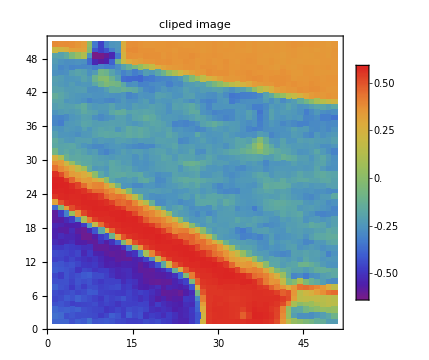
-Graphics--Graphics-

Elapsed time: 0.009205 seconds

-Graphics-

Elapsed time: 7.93377 seconds

-Graphics-

```mathematica
img=Reverse[Transpose@ImageData[ExampleData[{"TestImage","House"}]],2];
imgNorm=Table[Norm[img[[i,j]]],{j,1,Length[img[[1]]]},{i,1,Length[img]}]-2;
imgNorm=imgNorm-Mean@Mean[imgNorm];

(*位置(s,s)から画像を一部切り取りsubimgNormとする*)
s=150;
subimgNorm=imgNorm[[s;;s+50,s;;s+50]];

plotstyle={PlotLegends->Automatic,ColorFunction->"Rainbow",Frame->True,InterpolationOrder->0,ImageSize->Medium};

Row[{
ListDensityPlot[imgNorm,Evaluate[plotstyle],PlotLabel->"full image"],
ListDensityPlot[subimgNorm,Evaluate[plotstyle],PlotLabel->"cliped image"]
}]

{time,originalconvolve}=AbsoluteTiming[ListConvolve[subimgNorm,imgNorm,1,0]];
Print["Elapsed time: ",time," seconds"];


ListDensityPlot[originalconvolve,Evaluate[plotstyle],PlotRange->{All,All,{-150,150}}]

tediousConvolve[shifti_,shiftj_]:=Module[{sum=0,maxi=Length[subimgNorm],maxj=Length[subimgNorm[[1]]]},
Sum[subimgNorm[[shifti-i+1,shiftj-j+1]]*imgNorm[[i,j]]
,{i,If[-maxi+shifti+1<1,1,-maxi+shifti+1],shifti}
,{j,If[-maxj+shiftj+1<1,1,-maxj+shiftj+1],shiftj}]
];

{time,result}=AbsoluteTiming[ParallelTable[tediousConvolve[shifti,shiftj],{shifti,1,250},{shiftj,1,250}]];
Print["Elapsed time: ",time," seconds"];

ListDensityPlot[result,Evaluate[plotstyle],PlotRange->{All,All,{-150,150}} ]
```

```mathematica
(*DFTを使ったシンプルな効率的な畳み込みの計算*)
(*サイズ取得*)
nij=Dimensions[imgNorm];
mij=Dimensions[subimgNorm];
(*パディング*)
U=Fourier[ArrayPad[imgNorm,{{0,mij[[1]]-1},{0,mij[[2]]-1}},0],FourierParameters->{1,-1}];
V=Fourier[ArrayPad[subimgNorm,{{0,nij[[1]]-1},{0,nij[[2]]-1}},0],FourierParameters->{1,-1}];
(*逆変換で畳み込みを取得*)
{time,result}=AbsoluteTiming[Re@InverseFourier[U*V,FourierParameters->{1,-1}]];
Print["Elapsed time: ",time," seconds"];
(*可視化*)
ListDensityPlot[result,PlotLegends->Automatic,ColorFunction->"Rainbow",InterpolationOrder->0,PlotRange->{All,All,{-150,150}}]

(*逆変換で畳み込みを取得*)
{time,result}=AbsoluteTiming[Re@InverseFourier[U*Conjugate[V],FourierParameters->{1,-1}]];
Print["Elapsed time: ",time," seconds"];
(*可視化*)
ListDensityPlot[result,PlotLegends->Automatic,ColorFunction->"Rainbow",InterpolationOrder->0,PlotRange->{All,All,{-150,150}}]
```

Elapsed time: 0.001933 seconds

-Graphics-

Elapsed time: 0.001842 seconds

-Graphics-

## 畳み込み積分の表し方

Mathematicaにおいて，畳み込みの計算方法は
1. convolve[x_] = Integrate[f[T]*g[x - T], {T, -Infinity, Infinity}]
2. convolve[x_] = Convolve[g[t], f[t], t, x];
3. convolve[x_] = InverseFourierTransform[F[ω]*G[ω], ω, x, FourierParameters -> {1, -1}]
などが考えられる．

```mathematica
ClearAll["Global`*"];

(*離散信号の定義*)
f[x_]:=Piecewise[{{1/2,0<=x},{-1/2,True}}]
g[x_]:=Piecewise[{{1,-1<=x<=1},{0,True}}]

(*面白い例*)
(*f[x_]:=Sech[x]^2;
g[x_]:=HeavisideTheta[x]-1/2;
*)
(*convolve[x_]=Integrate[f[T]*g[x-T],{T,-Infinity,Infinity}];*)

(*convolve[x_]=Convolve[g[t],f[t],t,x];*)

F[w_]=FourierTransform[f[x],x,w,FourierParameters->{1,-1}];
G[w_]=FourierTransform[g[x],x,w,FourierParameters->{1,-1}];
convolve[x_]=InverseFourierTransform[F[w]*G[w],w,x,FourierParameters->{1,-1}];

Manipulate[
Plot[{f[x],g[shift-x],f[x]*g[shift-x],convolve[x]},{x,-5,5}
,AxesLabel->{"x",""}
,PlotLegends->{"f[x]","g[shift-x]","f[x]g[shift-x]","convolve[x]"}
,PlotLabel->"shift="<>ToString[shift]
,PlotStyle->{{Orange,Dashed},{Orange,DotDashed},Orange,Blue}
,Filling->{3->Axis}
,FillingStyle->Directive[Opacity[0.5],Blue]
,PlotRange->{{-5,5},{-1,1}}
,BaseStyle->Black
,Epilog->{Black,Line[{{shift,-6},{shift,6}}]}]
,{shift,-5,5}]

(*Export[FileNameJoin[{NotebookDirectory[],"sample_convolve.gif"}],%,"GIF",{"ImageSize"->700,"AnimationRepetitions"->∞,"AnimationRate"->10}]*)
```

## 離散畳み込み積分

```mathematica
ClearAll["Global`*"];

(*離散信号の定義*)
u={1,2,3,4,5,4,3,2,1};
v={1,-1,1,-1,1,-1,3};
m=Length[u];
n=Length[v];

(*２重和を使った畳み込みの計算*)
P[data_,j_]:=With[{i=j+1},Piecewise[{{data[[i]],Between[i,{1,Length[data]}]},{0,True}}]];
uv[k_]:=Sum[P[u,j]*P[v,k-j],{j,0,Length[u],1}]
Table[N@uv[k],{k,0,m+n-2}]

(*DFTを使ったシンプルな効率的な畳み込みの計算*)
U=Fourier[PadRight[u,m+n-1],FourierParameters->{1,-1}];
V=Fourier[PadRight[v,m+n-1],FourierParameters->{1,-1}];
W=U*V;
w=Re@InverseFourier[W,FourierParameters->{1,-1}]

Manipulate[
Column@{DiscretePlot[{P[u,i],P[v,shift-i],P[u,i]*P[v,shift-i]}
,{i,-20,20}
,AxesLabel->{"i",""}
,PlotRange->{{-8,20},{-2,15}}
,ExtentSize->Full
,ImageSize->Medium
,PlotLabel->Row[{"convolv[","shift = ",shift,"] = ",Sum[P[u,i]*P[v,shift-i],{i,0,10,1}],"\n"}
]],
DiscretePlot[{0,0,uv[i]},{i,-20,shift}
,AxesLabel->{"i",""}
,PlotRange->{{-8,20},{-2,15}}
,ExtentSize->Full
,ImageSize->Medium
,PlotLabel->Row[{"convolutions (integrations)=\n",
"({1,2,3,4,5,4,3,2,1}*{1,-1,1,-1,1,-1,3})[0;;",shift,"]=\n",
Style[Table[Sum[P[u,i]*P[v,X-i],{i,0,10,1}],{X,0,shift}]]}]
]}
,{shift,0,15,1}]

Export[FileNameJoin[{NotebookDirectory[],"sample_descrete_convolve.gif"}],%,"GIF",{"ImageSize"->700,"AnimationRepetitions"->∞,"AnimationRate"->10}]
```

{1.,1.,2.,2.,3.,1.,4.,5.,8.,9.,13.,10.,8.,5.,3.}

{1.,1.,2.,2.,3.,1.,4.,5.,8.,9.,13.,10.,8.,5.,3.}

/Users/tomoaki/Library/CloudStorage/Dropbox/code/cpp/builds/build_Fourier/sample_descrete_convolve.gif

Transpose::tperm: 置換{3,1,2}が式の次元{2,0}より長くなっています．

General::stop: この計算中に，Transpose::tpermのこれ以上の出力は表示されません．

Transpose::tperm: 置換{3,1,2}が式の次元{2,0}より長くなっています．

General::stop: この計算中に，Transpose::tpermのこれ以上の出力は表示されません．